```mathematica
Subscript[Data, GWP LFPC simplified]={251+116+73+16+42+93,176+167+10,809};
Subscript[Data, GWP LMOC simplified]={204+182+59+26+43+95,181+172+11,809};
Subscript[Data, GWP NCAC simplified]={297+145+62+38+40+89,170+160+10,809};
Subscript[Data, GWP NCOLTO simplified]={628+562+166+81+90+199,378+358+22,809};
Subscript[Data, GWP NMCC simplified]={230+117+50+15+35+76,146+138+9,809};

Subscript[Data, CED LFPC]={4262.1205,2661.0356,1411.6574,289.03668,763.24995,10743.908,3042.814,2874.4216,164.35926,13958.893}*0.277778;
Subscript[Data, CED LMOC]={3520,4048.3432,1168.9188,464.35352,783.40781,11027.661,3135.0205,2954.9055,168.79367,13958.893}*0.277778;
Subscript[Data, CED NCAC]={4819.9676,3282.1641,1209.0927,688.16771,733.26523,10321.828,2947.9373,2756.9475,157.92221,13958.893}*0.277778;
Subscript[Data, CED NCOLTO]={10164.267,10500,3264.5428,1454.7504,1636.1999,23032.012,6549.3196,6153.7608,352.32103,13958.893}*0.277778;
Subscript[Data, CED NMCC]={3724.2515,2585.2373,972.16691,268.79349,627.89505,8838.5814,2533.0008,2366.0224,135.32103,13958.893}*0.277778;

Subscript[Data, MRS LFPC simplified]={0.61764452+2.7022252+0.23215713+0.014306183+1.0749439+0.19512114,3.4928834+1.9789009+0.019090903,8.7291688};
Subscript[Data, MRS LMOC simplified]={0.819+6.7308854+0.18495116+0.022983679+1.1033337+0.2002744,3.5987284+2.0343101+0.019605975,8.7291688};
Subscript[Data, MRS NCAC simplified]={13.268177+4.480041+0.19410097+0.034061604+1.0327141+0.18745569,3.3839733+1.8980256+0.018343217,8.7291688};
Subscript[Data, MRS NCOLTO simplified]={30.30366+0.961+0.52259512+0.07200444+2.3043867+0.41828656,7.518044+4.2365679+0.040923319,8.7291687};
Subscript[Data, MRS NMCC simplified]={10.793242+4.6575952+0.15574665+0.013304224+0.8843131+0.16051832,2.9076626+1.6288924+0.015718011,8.7291688};

Subscript[Data, E lifetime 0.5 LFPC]=17673;
Subscript[Data, E lifetime 0.5 LMOC]=14094;
Subscript[Data, E lifetime 0.5 NCAC]=19699;
Subscript[Data, E lifetime 0.5 NCOLTO]=18013;
Subscript[Data, E lifetime 0.5 NMCC]=16334;

Subscript[Data, E lifetime 1 LFPC]=32217;
Subscript[Data, E lifetime 1 LMOC]=30552;
Subscript[Data, E lifetime 1 NCAC]=42746;
Subscript[Data, E lifetime 1 NCOLTO]=39117;
Subscript[Data, E lifetime 1 NMCC]=30756;

Subscript[Data, E lifetime 4 LFPC]=41169;
Subscript[Data, E lifetime 4 LMOC]=34479;
Subscript[Data, E lifetime 4 NCAC]=54166;
Subscript[Data, E lifetime 4 NCOLTO]=166158;
Subscript[Data, E lifetime 4 NMCC]=41457;

ClearAll[errorBar]
errorBar[type_: "Rectangle"]:=Module[{error=If[#3==={},0,#3[[1]]],x0=#[[1,1]],x1=#[[1,2]],y1=#[[2,2]]},{ChartElementData[type][##],{Black,Thickness[0.0029],Opacity[10],Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]&
```

```mathematica
Subscript[Componentcontribution, GWP LFPC]={251/1753+116/1753+73/1753+16/1753+42/1753+93/1753,176/1753+167/1753+10/1753,809/1753};
Subscript[Componentcontribution, GWP LMOC]={204/1782+182/1782+59/1782+26/1782+43/1782+95/1782,181/1782+172/1782+11/1782,809/1782};
Subscript[Componentcontribution, GWP NCAC]={297/1821+145/1821+62/1821+38/1821+40/1821+89/1821,170/1821+160/1821+10/1821,809/1821};
Subscript[Componentcontribution, GWP NCOLTO]={628/3295+562/3295+166/3295+81/3295+90/3295+199/3295,378/3295+358/3295+22/3295,809/3295};
Subscript[Componentcontribution, GWP NMCC]={230/1624+117/1624+50/1624+15/1624+35/1624+76/1624,146/1624+138/1624+9/1624,809/1624};

Rasterize[
Legended[
BarChart[
{
Subscript[Componentcontribution, GWP LFPC]*0.1022->0.0234,
Subscript[Componentcontribution, GWP LMOC]*0.1435->0.0726,
Subscript[Componentcontribution, GWP NCAC]*0.0924->0.0069,
Subscript[Componentcontribution, GWP NCOLTO]*0.1829->0.0445,
Subscript[Componentcontribution, GWP NMCC]*0.1057->0.0338,
0,0,0,0,0,

Subscript[Componentcontribution, GWP LFPC]*0.0601->0.0250,
Subscript[Componentcontribution, GWP LMOC]*0.0662->0.0335,
Subscript[Componentcontribution, GWP NCAC]*0.0426->0.0032,
Subscript[Componentcontribution, GWP NCOLTO]*0.0841->0.0205,
Subscript[Componentcontribution, GWP NMCC]*0.0587->0.0222,
0,0,0,0,0,

Subscript[Componentcontribution, GWP LFPC]*0.0522->0.0266,
Subscript[Componentcontribution, GWP LMOC]*0.0608->0.0342,
Subscript[Componentcontribution, GWP NCAC]*0.0338->0.0048,
Subscript[Componentcontribution, GWP NCOLTO]*0.0198->0.0048,
Subscript[Componentcontribution, GWP NMCC]*0.0492->0.0228,
0,0
},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,Automatic,errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Cell","Arial",16],Style["Module","Arial",16],Style["Inverter","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.835,0.65}],
FrameLabel->{None,Style["kg CO_2 eq / kWh",Bold]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Global warming potential per lifetime energy delivered",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,0.25,0.02],{#,#,{0.01,0}}&/@Range[0,0.25,0.02]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.91,11.68},None},
PlotRange->{Automatic,{Automatic,0.25}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 128 0 0","RGB 165 26 25","RGB 202 52 51"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["0.5 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["1 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["4 cycles per day",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}],
ImageResolution->650]
```

-Graphics-

```mathematica
max60={{0.5,0.1829},{1,0.0841},{1.5,0.0627},{2,0.0619},{2.5,0.0614},{3,0.0611},{3.5,0.0609},{4,0.0608}};
avg60={{0.5,0.1253},{1,0.0623},{1.5,0.0517},{2,0.0481},{2.5,0.0461},{3,0.0448},{3.5,0.0438},{4,0.0431}};
min60={{0.5,0.0924},{1,0.0426},{1.5,0.0348},{2,0.0344},{2.5,0.0321},{3,0.0266},{3.5,0.0227},{4,0.0198}};

max80={{0.5,0.1595},{1,0.1133},{1.5,0.1108},{2,0.1096},{2.5,0.1088},{3,0.1084},{3.5,0.1080},{4,0.1078}};
avg80={{0.5,0.1180},{1,0.0880},{1.5,0.0811},{2,0.0778},{2.5,0.0771},{3,0.0768},{3.5,0.0765},{4,0.0764}};
min80={{0.5,0.0806},{1,0.0630},{1.5,0.0483},{2,0.0358},{2.5,0.0346},{3,0.0344},{3.5,0.0343},{4,0.0342}};

Rasterize[
ListPlot[{max80,avg80,min80,max60,avg60,min60},
Joined->True,
PlotStyle->{{Interpreter["Color"]["RGB 31 78 121"],Opacity[0.5]},{Interpreter["Color"]["RGB 31 78 121"],Thick},{Interpreter["Color"]["RGB 31 78 121"],Opacity[0.5]},{Interpreter["Color"]["RGB 128 0 0"],Opacity[0.5]},{Interpreter["Color"]["RGB 128 0 0"],Thick},{Interpreter["Color"]["RGB 128 0 0"],Opacity[0.5]}},
Filling->{{{1->{3}},4->{6}}},
FillingStyle->{Opacity[0.35],Opacity[0.25]},
PlotRange->{{0.5,4},{0,0.20}},
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,0.19,0.02],{#,#,{0.01,0}}&/@Range[0,0.19,0.02]},{{#,#,{0.01,0}}&/@Range[0.5,4,0.5],None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},

PlotLegends->Placed[LineLegend[{None,Style["80% of the initial storage capacity retained","Arial",16],None,None,Style["60% of the initial storage capacity retained","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.52,0.85}],
PlotLabel->Style["Influence of final capacity retention on GWP / kWh delivered",Black,Bold],
FrameLabel->{Style["cycles / day",Bold],Style["kg CO_2 eq / kWh",Bold]},
BaseStyle->{Directive[FontFamily->"Arial"],16},
ImageSize->Large],
ImageResolution->1000]
```

-Graphics-

```mathematica
Rasterize[
Legended[
BarChart[
{
{944/1753*0.1022,809/1753*0.1022,1.15*0.041}->(0.0234+0.02*0.041),
{973/1782*0.1435,809/1782*0.1435,1.14*0.041}->0.0726,
{337/607*0.0924,809/1821*0.0924,1.16*0.041}->0.0069,
{2484/3295*0.1829,809/3295*0.1829,1.22*0.041}->0.0445,
{102/203*0.1057,809/1624*0.1057,1.15*0.041}->(0.0338+0.02*0.041),
0,0,0,0,0,

{944/1753*0.0601,809/1753*0.0601,1.15*0.041}->0.0250,
{973/1782*0.0662,809/1782*0.0662,1.14*0.041}->0.0335,
{337/607*0.0426,809/1821*0.0426,1.16*0.041}->0.0032,
{2484/3295*0.0841,809/3295*0.0841,1.22*0.041}->0.0205,
{102/203*0.0587,809/1624*0.0587,1.15*0.041}->0.0222,
0,0,0,0,0,

{944/1753*0.0522,809/1753*0.0522,1.15*0.041}->(0.0266+0.02*0.041),
{973/1782*0.0608,809/1782*0.0608,1.14*0.041}->0.0342,
{337/607*0.0338,809/1821*0.0338,1.16*0.041}->0.0048,
{2484/3295*0.0198,809/3295*0.0198,1.22*0.041}->0.0048,
{102/203*0.0492,809/1624*0.0492,1.15*0.041}->(0.0228+0.02*0.041),
0,0
},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,Automatic,errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Battery module","Arial",16],Style["Battery inverter","Arial",16],Style["Rooftop solar PV","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.83,0.70}],
FrameLabel->{None,Style["kg CO_2 eq / kWh",Bold]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["GWP per lifetime energy delivered by PV and battery system",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,0.28,0.02],{#,#,{0.01,0}}&/@Range[0,0.28,0.02]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.91,11.68},None},
PlotRange->{Automatic,{Automatic,0.29}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 128 0 0","RGB 202 52 51","RGB 31 78 121"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["0.5 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["1 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["4 cycles per day",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}],
ImageResolution->650]
```

-Graphics-

```mathematica
Rasterize[
Legended[
BarChart[
{
{944/1753*0.0601,809/1753*0.0601,1.15*0.041}->(0.0250+0.02*0.041),
{973/1782*0.0662,809/1782*0.0662,1.14*0.041}->0.0335,
{337/607*0.0426,809/1821*0.0426,1.16*0.041}->0.0032,
{2484/3295*0.0841,809/3295*0.0841,1.22*0.041}->0.0205,
{102/203*0.0587,809/1624*0.0587,1.15*0.041}->(0.0222+0.02*0.041),
0,0,0,0,0,

{944/1753*0.0601,809/1753*0.0601,1.15*0.439}->(0.0250+0.02*0.439),
{973/1782*0.0662,809/1782*0.0662,1.14*0.439}->0.0335,
{337/607*0.0426,809/1821*0.0426,1.16*0.439}->0.0032,
{2484/3295*0.0841,809/3295*0.0841,1.22*0.439}->0.0205,
{102/203*0.0587,809/1624*0.0587,1.15*0.439}->(0.0222+0.02*0.439),
0,0
},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,Automatic,errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","",""},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Battery module","Arial",16],Style["Battery inverter","Arial",16],Style["Power generation","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.25,0.70}],
FrameLabel->{None,Style["kg CO_2 eq / kWh",Bold]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["GWP / kWh delivered by battery system and its power source",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,0.65,0.05],{#,#,{0.01,0}}&/@Range[0,0.65,0.05]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.75,11.68},None},
PlotRange->{Automatic,{Automatic,0.67}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 128 0 0","RGB 202 52 51","RGB 31 78 121"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["Rooftop solar PV",Black,Bold,16,FontFamily->"Arial"],{0.25,Top}],
Placed[Style["US grid",Black,Bold,16,FontFamily->"Arial"],{0.75,Top}]}],
ImageResolution->650]
```

-Graphics-

```mathematica
Subscript[Componentcontribution, MRS LFPC]={(0.61764452+2.7022252+0.23215713+0.014306183+1.0749439+0.19512114)/19.05644208,(3.4928834+1.9789009+0.019090903)/19.05644208,8.7291688/19.05644208};
Subscript[Componentcontribution, MRS LMOC]={(0.819+6.7308854+0.18495116+0.022983679+1.1033337+0.2002744)/23.44324161,(3.5987284+2.0343101+0.019605975)/23.44324161,8.7291688/23.44324161};
Subscript[Componentcontribution, MRS NCAC]={(13.268177+4.480041+0.19410097+0.034061604+1.0327141+0.18745569)/33.22606128,(3.3839733+1.8980256+0.018343217)/33.22606128,8.7291688/33.22606128};
Subscript[Componentcontribution, MRS NCOLTO]={(30.30366+0.961+0.52259512+0.07200444+2.3043867+0.41828656)/55.10663674,(7.518044+4.2365679+0.040923319)/55.10663674,8.7291687/55.10663674};
Subscript[Componentcontribution, MRS NMCC]={(10.793242+4.6575952+0.15574665+0.013304224+0.8843131+0.16051832)/29.94616131,(2.9076626+1.6288924+0.015718011)/29.94616131,8.7291688/29.94616131};

Rasterize[
Legended[
BarChart[
{
Subscript[Componentcontribution, MRS LFPC]*0.001111->0.000255,
Subscript[Componentcontribution, MRS LMOC]*0.001891->0.000966,
Subscript[Componentcontribution, MRS NCAC]*0.001681->0.000181,
Subscript[Componentcontribution, MRS NCOLTO]*0.003059->0.000830,
Subscript[Componentcontribution, MRS NMCC]*0.001952->0.000699,
0,0,0,0,0,

Subscript[Componentcontribution, MRS LFPC]*0.000653->0.000272,
Subscript[Componentcontribution, MRS LMOC]*0.000872->0.000446,
Subscript[Componentcontribution, MRS NCAC]*0.000774->0.000084,
Subscript[Componentcontribution, MRS NCOLTO]*0.001407->0.000382,
Subscript[Componentcontribution, MRS NMCC]*0.001088->0.000448,
0,0,0,0,0,

Subscript[Componentcontribution, MRS LFPC]*0.000567->0.000289,
Subscript[Componentcontribution, MRS LMOC]*0.000801->0.000455,
Subscript[Componentcontribution, MRS NCAC]*0.000615->0.000111,
Subscript[Componentcontribution, MRS NCOLTO]*0.000332->0.000090,
Subscript[Componentcontribution, MRS NMCC]*0.000914->0.000453,
0,0
},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,Automatic,errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Cell","Arial",16],Style["Module","Arial",16],Style["Inverter","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.84,0.65}],
FrameLabel->{None,Style["USD2013 / kWh",Bold]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Mineral resource scarcity per lifetime energy delivered",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,0.004,0.0005],{#,#,{0.01,0}}&/@Range[0,0.004,0.0005]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.91,11.68},None},
PlotRange->{Automatic,{Automatic,0.0042}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 47 79 79","RGB 112 128 144","RGB 192 192 192"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["0.5 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["1 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["4 cycles per day",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}],
ImageResolution->650]
```

-Graphics-

```mathematica
Rasterize[
Legended[
BarChart[
{{
1.6039->0.2983,
1.2458->0.6391,
1.7506->0.1697,
0.8719->0.2303,
1.7081->0.5964},

{2.8936->0.7560,
2.7004->1.3854,
3.7987->0.3683,
1.8962->0.5008,
3.2613->1.4660},

{3.6974->1.8565,
3.0518->1.7411,
4.8413->0.7059,
8.0423->2.1241,
4.5275->3.7582}
},
BarSpacing->{Automatic,1},
ChartElementFunction->{errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Energy delivered on energy invested (without charge energy)",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,10,1],{#,#,{0.01,0}}&/@Range[0,10,1]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{6.37,12.22},None},
PlotRange->{Automatic,{Automatic,10.55}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 255 125 49","RGB 240 116 178","RGB 255 192 0","RGB 0 176 240","RGB 146 208 80"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["0.5 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["1 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["4 cycles per day",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}],
ImageResolution->650]
```

-Graphics-

```mathematica
Rasterize[
Legended[
BarChart[
{
{1.6039,2.5065-1.6039}->0.2983,
{1.2458,1.8968-1.2458}->0.6391,
{1.7506,2.7170-1.7506}->0.1697,
{0.8719,1.0839-0.8719}->0.2303,
{1.7081,2.9969-1.7081}->0.5964,

0,0,0,0,0,

{2.8936,4.4925-2.8936}->0.7560,
{2.7004,4.1117-2.7004}->1.3854,
{3.7987,5.8955-3.7987}->0.3683,
{1.8962,2.3575-1.8962}->0.5008,
{3.2613,5.7755-3.2613}->1.4660,

0,0,0,0,0,

{3.6974,5.7355-3.6974}->1.8565,
{3.0518,4.6498-3.0518}->1.7411,
{4.8413,7.5218-4.8413}->0.7059,
{8.0423,9.9987-8.0423}->2.1241,
{4.5275,8.1989-4.5275}->3.7582,
0,0
},
ChartLayout->"Stacked",
ChartElementFunction->{errorBar[],Automatic},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","",""},
Below,Rotate[#,Pi/2.4]&],None},
LabelStyle->Directive[Black,Black],
ChartLegends->Placed[SwatchLegend[Automatic,{Style["EDOEI of a system with an inverter","Arial",16],Style["Added EDOEI in a system without an inverter","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.335,0.75}],
PlotLabel->Style["Energy delivered on energy invested (without charge energy)",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,10,1],{#,#,{0.01,0}}&/@Range[0,10,1]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.9,11.68},None},
PlotRange->{Automatic,{Automatic,10.55}},
GridLinesStyle->Directive[Black,Dashed],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ChartStyle->Interpreter["Color"][{"RGB 191 144 0","RGB 175 171 171"}],
ImageSize->Large],
{Placed[Style["0.5 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["1 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["4 cycles per day",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}]
/.x:{{_Directive,__}..}:>x[[{2,1}]],
ImageResolution->650]
```

-Graphics-

```mathematica
Rasterize[
Legended[
BarChart[
{{
0.5029->0.0357,
0.4543->0.0957,
0.5171->0.0144,
0.3839->0.0459,
0.5087->0.0554},

{0.6201->0.0519,
0.6112->0.0810,
0.6586->0.0108,
0.5375->0.0416,
0.6317->0.0587},

{0.6712->0.0678,
0.6526->0.0941,
0.7176->0.0193,
0.7283->0.0180,
0.6870->0.0697}
},
BarSpacing->{Automatic,1},
ChartElementFunction->{errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Energy delivered on energy invested (with charge energy)",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,1,0.1],{#,#,{0.01,0}}&/@Range[0,1,0.1]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{6.37,12.22},None},
PlotRange->{Automatic,{Automatic,1.02}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 192 0 0","RGB 112 48 160","RGB 191 144 0","RGB 0 112 192","RGB 0 176 80"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["0.5 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["1 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["4 cycles per day",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}],
ImageResolution->650]
```

-Graphics-

```mathematica
Rasterize[
Legended[
BarChart[
{
{0.5029,0.5664-0.5029}->0.0357,
{0.4543,0.5225-0.4543}->0.0957,
{0.5171,0.5765-0.5171}->0.0144,
{0.3839,0.4188-0.3839}->0.0459,
{0.5087,0.5811-0.5087}->0.0554,

0,0,0,0,0,

{0.6201,0.6736-0.6201}->0.0519,
{0.6112,0.6666-0.6112}->0.0810,
{0.6586,0.7010-0.6586}->0.0108,
{0.5375,0.5678-0.5375}->0.0416,
{0.6317,0.6900-0.6317}->0.0587,

0,0,0,0,0,

{0.6712,0.7239-0.6712}->0.0678,
{0.6526,0.7096-0.6526}->0.0941,
{0.7176,0.7568-0.7176}->0.0193,
{0.7283,0.7409-0.7283}->0.0180,
{0.6870,0.7426-0.6870}->0.0697,
0,0
},
ChartLayout->"Stacked",
ChartElementFunction->{errorBar[],Automatic},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","",""},
Below,Rotate[#,Pi/2.4]&],None},
LabelStyle->Directive[Black,Black],
ChartLegends->Placed[SwatchLegend[Automatic,{Style["EDOEI of a system with an inverter","Arial",16],Style["Added EDOEI in a system without an inverter","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.335,0.82}],
PlotLabel->Style["Energy delivered on energy invested (with charge energy)",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,1,0.1],{#,#,{0.01,0}}&/@Range[0,1,0.1]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.9,11.68},None},
PlotRange->{Automatic,{Automatic,1.02}},
GridLinesStyle->Directive[Black,Dashed],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ChartStyle->Interpreter["Color"][{"RGB 112 48 160","RGB 175 171 171"}],
ImageSize->Large],
{Placed[Style["0.5 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["1 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["4 cycles per day",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}]
/.x:{{_Directive,__}..}:>x[[{2,1}]],
ImageResolution->650]
```

-Graphics-

```mathematica
Subscript[λ, LFPC]=6850;
Subscript[λ, LMOC]=5840;
Subscript[λ, NCAC]=9281;
Subscript[λ, NCOLTO]=30000;
Subscript[λ, NMCC]=7250;
Subscript[Y, LFPC]=19;
Subscript[Y, LMOC]=15;
Subscript[Y, NCAC]=21;
Subscript[Y, NCOLTO]=20;
Subscript[Y, NMCC]=18;

Rasterize[
Plot[
{If[Subscript[Y, LFPC]*365*n<Subscript[λ, LFPC],Subscript[Y, LFPC]*365*n,Subscript[λ, LFPC]],
If[Subscript[Y, LMOC]*365*n<Subscript[λ, LMOC],Subscript[Y, LMOC]*365*n,Subscript[λ, LMOC]],
If[Subscript[Y, NCAC]*365*n<Subscript[λ, NCAC],Subscript[Y, NCAC]*365*n,Subscript[λ, NCAC]],
If[Subscript[Y, NCOLTO]*365*n<Subscript[λ, NCOLTO],Subscript[Y, NCOLTO]*365*n,Subscript[λ, NCOLTO]],
If[Subscript[Y, NMCC]*365*n<Subscript[λ, NMCC],Subscript[Y, NMCC]*365*n,Subscript[λ, NMCC]]},
{n,0,5},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Impact of the intensity of the cycling on the total cycles performed",Black,Bold,16],
FrameLabel->{Style["Cycles per day",Bold,"Arial",16],Style["Total cycles performed",Bold,"Arial",16]},
PlotLegends->Placed[LineLegend[Automatic,{Style["LFP-C","Arial",16],Style["LMO-C","Arial",16],Style["NCA-C","Arial",16],Style["NCO-LTO","Arial",16],Style["NMC-C","Arial",16]},Spacings->0.15,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.19,0.71}],
PlotRange->{{0,5},{0,35000}},
ImageSize->Large,
Frame->True,
FrameStyle->Black,
BaseStyle->{Directive[FontFamily->"Arial"],16},
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,35000,5000],{#,#,{0.01,0}}&/@Range[0,35000,5000]},{{#,#,{0.01,0}}&/@Range[0,5,1],{#,#,{0.01,0}}&/@Range[0,5,1]}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}}},
PlotStyle->{Directive[Interpreter["Color"]["RGB 185 0 0"],Thickness[0.005],Opacity[0.8]],Directive[Interpreter["Color"]["RGB 240 116 178"],Thickness[0.005],Opacity[0.8]],Directive[Interpreter["Color"]["RGB 255 192 0"],Thickness[0.005],Opacity[0.8]],Directive[Interpreter["Color"]["RGB 0 112 192"],Thickness[0.005],Opacity[0.8]],Directive[Interpreter["Color"]["RGB 0 176 80"],Thickness[0.005],Opacity[0.8]]}],
ImageResolution->1000]
```

-Graphics-

```mathematica
Subscript[Data, E lifetime 0.5 LFPC]={17673,1040.7+1949};
Subscript[Data, E lifetime 0.5 LMOC]={14094,823+1540};
Subscript[Data, E lifetime 0.5 NCAC]={19699,1165+2182};
Subscript[Data, E lifetime 0.5 NCOLTO]={18013,1097+2054};
Subscript[Data, E lifetime 0.5 NMCC]={16334,957+1792};

Subscript[Data, E lifetime 1 LFPC]={32217,874.2+1637};
Subscript[Data, E lifetime 1 LMOC]={30552,823+1540};
Subscript[Data, E lifetime 1 NCAC]={42746,1165+2182};
Subscript[Data, E lifetime 1 NCOLTO]={39117,1097+2054};
Subscript[Data, E lifetime 1 NMCC]={30756,831+1556};

Subscript[Data, E lifetime 4 LFPC]={41169,263.5+493};
Subscript[Data, E lifetime 4 LMOC]={34479,219+411};
Subscript[Data, E lifetime 4 NCAC]={54166,349+653};
Subscript[Data, E lifetime 4 NCOLTO]={166158,1097+2054};
Subscript[Data, E lifetime 4 NMCC]={41457,265+495};

Rasterize[
Legended[
BarChart[
{
Subscript[Data, E lifetime 0.5 LFPC]->2758,
Subscript[Data, E lifetime 0.5 LMOC]->6644,
Subscript[Data, E lifetime 0.5 NCAC]->2276,
Subscript[Data, E lifetime 0.5 NCOLTO],
Subscript[Data, E lifetime 0.5 NMCC]->3863,
0,0,0,0,0,

Subscript[Data, E lifetime 1 LFPC]->9270,
Subscript[Data, E lifetime 1 LMOC]->14402,
Subscript[Data, E lifetime 1 NCAC]->4946,
Subscript[Data, E lifetime 1 NCOLTO],
Subscript[Data, E lifetime 1 NMCC]->9744,
0,0,0,0,0,

Subscript[Data, E lifetime 4 LFPC]->20578,
Subscript[Data, E lifetime 4 LMOC]->18285,
Subscript[Data, E lifetime 4 NCAC]->5580,
Subscript[Data, E lifetime 4 NCOLTO],
Subscript[Data, E lifetime 4 NMCC]->26265,
0,0
},
ChartLayout->"Stacked",
ChartElementFunction->{errorBar[],Automatic},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Lifetime energy delivered","Arial",16],Style["Loss due to self-consumption","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.3,0.70}],
FrameLabel->{None,Style["kWh",Bold]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Lifetime energy delivered",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,180000,20000],{#,#,{0.01,0}}&/@Range[0,180000,20000]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.9,11.68},None},
PlotRange->{Automatic,{Automatic,185000}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->{Interpreter["Color"]["RGB 255 192 0"],Directive[Red]},
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["0.5 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["1 cycle per day",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["4 cycles per day",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}]
/.x:{{_Directive,__}..}:>x[[{2,1}]],
ImageResolution->650]
```

-Graphics-

```mathematica
Subscript[Data, GWP LFPC]={251,116,73,16,42,93,176,167,10,809};
Subscript[Data, GWP LMOC]={204,182,59,26,43,95,181,172,11,809};
Subscript[Data, GWP NCAC]={297,145,62,38,40,89,170,160,10,809};
Subscript[Data, GWP NCOLTO]={628,562,166,81,90,199,378,358,22,809};
Subscript[Data, GWP NMCC]={230,117,50,15,35,76,146,138,9,809};

Rasterize[
BarChart[
{
Subscript[Data, GWP LFPC]->175.89,
Subscript[Data, GWP LMOC]->69.68,
Subscript[Data, GWP NCAC]->256.44,
Subscript[Data, GWP NCOLTO]->801.79,
Subscript[Data, GWP NMCC]->70.26,
0},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Positive electrode","Arial",16],Style["Negative electrode","Arial",16],Style["Electrolyte","Arial",16],Style["Separator","Arial",16],Style["Cell container","Arial",16],Style["Final cell assembly","Arial",16],Style["BMS","Arial",16],Style["Module casing","Arial",16],Style["Final module assembly","Arial",16],Style["Battery inverter","Arial",16]},Spacings->0.15,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.3,0.79}],
FrameLabel->{None,Style["kg CO_2 eq",Bold]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Global warming potential per battery system",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,4300,500],{#,#,{0.01,0}}&/@Range[0,4300,500]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.87,11.6},None},
PlotRange->{Automatic,{Automatic,4100}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 110 0 0","RGB 185 0 0","RGB 230 10 10","RGB 255 103 4","RGB 255 192 0","RGB 255 220 80","RGB 56 87 35","RGB 169 209 142","RGB 226 240 217","RGB 31 78 121"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
AspectRatio->1.5],
ImageResolution->650]
```

-Graphics-

```mathematica
Subscript[Data, MRS LFPC]={0.61764452,2.7022252,0.23215713,0.014306183,1.0749439,0.19512114,3.4928834,1.9789009,0.019090903,8.7291688};
Subscript[Data, MRS LMOC]={0.819,6.7308854,0.18495116,0.022983679,1.1033337,0.2002744,3.5987284,2.0343101,0.019605975,8.7291688};
Subscript[Data, MRS NCAC]={13.268177,4.480041,0.19410097,0.034061604,1.0327141,0.18745569,3.3839733,1.8980256,0.018343217,8.7291688};
Subscript[Data, MRS NCOLTO]={30.30366,0.961,0.52259512,0.07200444,2.3043867,0.41828656,7.518044,4.2365679,0.040923319,8.7291687};
Subscript[Data, MRS NMCC]={10.793242,4.6575952,0.15574665,0.013304224,0.8843131,0.16051832,2.9076626,1.6288924,0.015718011,8.7291688};

Rasterize[
BarChart[
{
Subscript[Data, MRS LFPC]->1.92,
Subscript[Data, MRS LMOC]->1.05,
Subscript[Data, MRS NCAC]->6.21,
Subscript[Data, MRS NCOLTO]->14.96,
Subscript[Data, MRS NMCC]->7.03,
0},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Positive electrode","Arial",16],Style["Negative electrode","Arial",16],Style["Electrolyte","Arial",16],Style["Separator","Arial",16],Style["Cell container","Arial",16],Style["Final cell assembly","Arial",16],Style["BMS","Arial",16],Style["Module casing","Arial",16],Style["Final module assembly","Arial",16],Style["Battery inverter","Arial",16]},Spacings->0.15,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.3,0.79}],
FrameLabel->{None,Style["USD (2013)",Bold]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Mineral resource scarcity per battery system",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,80,10],{#,#,{0.01,0}}&/@Range[0,80,10]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.87,11.6},None},
PlotRange->{Automatic,{Automatic,70}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 110 0 0","RGB 185 0 0","RGB 230 10 10","RGB 255 103 4","RGB 255 192 0","RGB 255 220 80","RGB 56 87 35","RGB 169 209 142","RGB 226 240 217","RGB 31 78 121"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
AspectRatio->1.5],
ImageResolution->650]
```

-Graphics-

```mathematica
Subscript[Data, components LFPC]={31.8,2.5,2.0,2.8,12.2,1.2,0.0,6.6,13.1,2.1,2.6,6.4,6.6,25.0,23.8};
Subscript[Data, components LMOC]={16.1,0.3,0.7,10.2,15.7,0.6,0.5,16.6,12.6,1.5,4.2,6.6,6.8,25.7,23.8};
Subscript[Data, components NCAC]={20.9,0.4,0.9,5.3,14.7,0.3,0.0,11.0,12.3,1.7,6.3,6.2,6.4,24.0,23.8};
Subscript[Data, components NCOLTO]={43.2,0.9,1.8,11.0,41.0,1.5,2.4,11.3,33.7,4.5,13.4,13.8,14.2,53.5,23.8};
Subscript[Data, components NMCC]={21.9,1.5,0.8,3.5,9.8,0.5,0.0,11.6,10.0,1.3,2.4,5.3,5.5,20.6,23.8};

Rasterize[
BarChart[
{
Subscript[Data, components LFPC]->21.4,
Subscript[Data, components LMOC]->8.4,
Subscript[Data, components NCAC]->28.0,
Subscript[Data, components NCOLTO]->79.4,
Subscript[Data, components NMCC]->31.4},
ChartLayout->"Stacked",
BarSpacing->{Automatic,0.7},
ChartElementFunction->{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Cathode's active material","Arial",16],Style["Cathode's binder","Arial",16],Style["Cathode's conductive carbon","Arial",16],Style["Cathode's current collector","Arial",16],Style["Anode's active material","Arial",16],Style["Anode's binder","Arial",16],Style["Anode's conductive carbon","Arial",16],Style["Anode's current collector","Arial",16],Style["Electrolyte (carbonate solvent)","Arial",16],Style["Electrolyte (lithium ions)","Arial",16],Style["Separator","Arial",16],Style["Cell container","Arial",16],Style["BMS","Arial",16],Style["Module casing","Arial",16],Style["Battery inverter","Arial",16]},Spacings->0.15,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LegendLayout->{"ReversedColumn",1}],{0.33,0.72}],
FrameLabel->{None,Style["kg",Bold]},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Component mass in battery systems",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,350,50],{#,#,{0.01,0}}&/@Range[0,350,50]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.87,11.6},None},
PlotRange->{Automatic,{Automatic,350}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 192 0 0","RGB 200 20 20","RGB 200 50 50","RGB 211 76 76","RGB 31 78 121","RGB 46 90 150","RGB 46 117 182","RGB 157 195 230","RGB 255 192 0","RGB 255 220 80","RGB 84 130 53","RGB 169 209 142","RGB 118 113 113","RGB 175 171 171","RGB 208 206 206"}],
ImageSize->200,
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
AspectRatio->1.4],
ImageResolution->650]
```

-Graphics-

```mathematica
Subscript[Data, recovery LFPC]={0.1283,0.0000,0.0856,0.0000,0.0982,0.0000,0.0000,0.1015,0.0000,0.1059,0.0123,0.0319,0.3035+0.1327};
Subscript[Data, recovery LMOC]={0.1900,0.0000,0.1692,0.0000,0.0000,0.0829,0.0000,0.1015,0.0000,0.1327,0.0053,0.0366,0.1619+0.1199};
Subscript[Data, recovery NCAC]={0.1549,0.0174,0.1281,0.0000,0.0000,0.0000,0.0927,0.1015,0.0000,0.1336,0.0137,0.0439,0.1876+0.1267};
Subscript[Data, recovery NCOLTO]={0.1948,0.0211,0.0285,0.0000,0.0000,0.0000,0.0845,0.1015,0.0868,0.0000,0.0227,0.0431,0.2620+0.1551};
Subscript[Data, recovery NMCC]={0.1407,0.0284,0.1508,0.0000,0.0000,0.0529,0.0568,0.1015,0.0000,0.1032,0.0168,0.0330,0.1959+0.1201};
Subscript[Data, recovery inverter]={0.4433,0.0000,0.1700,0.0002,0.0031,0.0000,0.0000,0.0806,0.0000,0.0000,0.0000,0.0963,0.2065+0.0000};

Rasterize[
BarChart[
{
Subscript[Data, recovery LFPC],
Subscript[Data, recovery LMOC],
Subscript[Data, recovery NCAC],
Subscript[Data, recovery NCOLTO],
Subscript[Data, recovery NMCC],
Subscript[Data, recovery inverter]},
ChartLayout->"Stacked",
BarSpacing->0.7,
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","Inverter"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Aluminium","Arial",16],Style["Cobalt","Arial",16],Style["Copper","Arial",16],Style["Gold","Arial",16],Style["Iron","Arial",16],Style["Manganese","Arial",16],Style["Nickel","Arial",16],Style["Steel","Arial",16],Style["Titanium","Arial",16],Style["Graphite","Arial",16],Style["Lithium","Arial",16],Style["Plastics","Arial",16],Style["Other","Arial",16]},Spacings->0.5,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LegendLayout->{"ReversedColumn",1}],Right],
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Materials composing the batteries",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,ToString[100 #]<>" %",{0.02,0}}&/@Range[0,1,0.1],{#,ToString[100 #]<>" %",{0.02,0}}&/@Range[0,1,0.1]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
PlotRange->{Automatic,{Automatic,0.95}},
ChartStyle->Interpreter["Color"][{"RGB 192 0 0","RGB 255 0 0","RGB 255 192 0","RGB 255 255 0","RGB 146 208 80","RGB 0 176 80","RGB 0 176 240","RGB 0 112 192","RGB 0 32 96","RGB 82 82 82","RGB 124 124 124","RGB 175 171 171","RGB 112 48 160"}],
ImageSize->Small,
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ChartElementFunction->System`BarFunctionDump`TextureBar,
AspectRatio->1.3],
ImageResolution->150]
```

-Graphics-

```mathematica
Subscript[Mass, LFP]={0.00000,0.00000,0.35400,0.00000,0.00000,0.00000,0.04399,0.40567,0.19634,0.00000};
Subscript[Mass, LMO]={0.00000,0.00000,0.00000,0.60768,0.00000,0.00000,0.03838,0.35394,0.00000,0.00000};
Subscript[Mass, NCA]={0.01404,0.09200,0.00000,0.00000,0.48869,0.00000,0.07223,0.33303,0.00000,0.00000};
Subscript[Mass, NCO]={0.00000,0.12067,0.00000,0.00000,0.48070,0.00000,0.07105,0.32759,0.00000,0.00000};
Subscript[Mass, NMC]={0.00000,0.12255,0.00000,0.22848,0.24410,0.00000,0.07216,0.33270,0.00000,0.00000};
Subscript[Mass, LTO]={0.00000,0.00000,0.00000,0.00000,0.00000,0.52133,0.06047,0.41821,0.00000,0.00000};

Subscript[GWP, LFP]={0.00000,0.00000,0.05585,0.00000,0.00000,0.00000,0.16725,0.00000,0.28129,0.49561};
Subscript[GWP, LMO]={0.00000,0.00000,0.00000,0.49152,0.00000,0.00000,0.03677,0.00000,0.00000,0.47171};
Subscript[GWP, NCA]={0.00456,0.12089,0.00000,0.00000,0.72110,0.00000,0.03298,0.00000,0.00000,0.12047};
Subscript[GWP, NCO]={0.00000,0.15644,0.00000,0.00000,0.69530,0.00000,0.03180,0.00000,0.00000,0.11646};
Subscript[GWP, NMC]={0.00000,0.26325,0.00000,0.02014,0.60071,0.00000,0.05495,0.00000,0.00000,0.06095};
Subscript[GWP, LTO]={0.00000,0.00000,0.00000,0.00000,0.00000,0.67964,0.04052,0.00000,0.00000,0.27984};

Subscript[MRS, LFP]={0.00000,0.00000,0.12870,0.00000,0.00000,0.00000,0.12963,0.00000,0.57315,0.16852};
Subscript[MRS, LMO]={0.00000,0.00000,0.00000,0.87895,0.00000,0.00000,0.02559,0.00000,0.00000,0.09546};
Subscript[MRS, NCA]={0.00061,0.32045,0.00000,0.00000,0.66989,0.00000,0.00123,0.00000,0.00000,0.00782};
Subscript[MRS, NCO]={0.00000,0.38897,0.00000,0.00000,0.60377,0.00000,0.00111,0.00000,0.00000,0.00615};
Subscript[MRS, NMC]={0.00000,0.53942,0.00000,0.01834,0.43154,0.00000,0.00158,0.00000,0.00000,0.00912};
Subscript[MRS, LTO]={0.00000,0.00000,0.00000,0.00000,0.00000,0.74455,0.15918,0.00000,0.00000,0.09627};

Rasterize[
Legended[
BarChart[
{
Subscript[Mass, LFP],
Subscript[Mass, LMO],
Subscript[Mass, NCA],
Subscript[Mass, NCO],
Subscript[Mass, NMC],
Subscript[Mass, LTO],
0,0,0,0,0,

Subscript[GWP, LFP],
Subscript[GWP, LMO],
Subscript[GWP, NCA],
Subscript[GWP, NCO],
Subscript[GWP, NMC],
Subscript[GWP, LTO],
0,0,0,0,0,

Subscript[MRS, LFP],
Subscript[MRS, LMO],
Subscript[MRS, NCA],
Subscript[MRS, NCO],
Subscript[MRS, NMC],
Subscript[MRS, LTO],
0,0
},
ChartLayout->"Stacked",
ChartLabels->{Placed[
{"LFP","LMO","NCA","NCO","NMC","LTO","","","","","",
"LFP","LMO","NCA","NCO","NMC","LTO","","","","","",
"LFP","LMO","NCA","NCO","NMC","LTO"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Aluminium","Arial",16],Style["Cobalt","Arial",16],Style["Iron","Arial",16],Style["Manganese","Arial",16],Style["Nickel","Arial",16],Style["Titanium","Arial",16],Style["Lithium","Arial",16],Style["Oxygen","Arial",16],Style["Phosphate","Arial",16],Style["Assembly","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],Right],
FrameLabel->{None,None},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Impact contribution within the active materials",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,ToString[100 #]<>" %",{0.02,0}}&/@Range[0,1,0.1],{#,ToString[100 #]<>" %",{0.02,0}}&/@Range[0,1,0.1]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{6.95,13.79},None},
PlotRange->{Automatic,{Automatic,1.03}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 192 0 0","RGB 255 0 0","RGB 255 192 0","RGB 255 255 0","RGB 146 208 80","RGB 0 176 80","RGB 0 176 240","RGB 0 112 192","RGB 0 32 96","RGB 112 48 160"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["Mass",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["GWP",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["MRS",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}],
ImageResolution->800]
```

-Graphics-

```mathematica
Subscript[Mass, LFPC]={0.5395,0.0415,0.0333,0.0000,0.0474,0.0000,0.2062,0.0208,0.0000,0.0000,0.1112,0.0000};
Subscript[Mass, LMOC]={0.2659,0.0042,0.0113,0.0000,0.1677,0.0000,0.2586,0.0097,0.0083,0.0000,0.2743,0.0000};
Subscript[Mass, NCAC]={0.3898,0.0083,0.0166,0.0000,0.0994,0.0000,0.2752,0.0056,0.0000,0.0000,0.2051,0.0000};
Subscript[Mass, NCOLTO]={0.3817,0.0081,0.0162,0.0000,0.0974,0.0000,0.3619,0.0129,0.0215,0.0000,0.1002,0.0000};
Subscript[Mass, NMCC]={0.4431,0.0293,0.0171,0.0000,0.0702,0.0000,0.1973,0.0092,0.0000,0.0000,0.2338,0.0000};

Subscript[GWP, LFPC]={0.2970,0.1267,0.0129,0.1738,0.0695,0.0041,0.0768,0.0114,0.0000,0.1450,0.0809,0.0019};
Subscript[GWP, LMOC]={0.1909,0.0118,0.0045,0.0777,0.2396,0.0039,0.0943,0.0063,0.0030,0.1711,0.1951,0.0018};
Subscript[GWP, NCAC]={0.4457,0.0193,0.0049,0.0890,0.1097,0.0034,0.0769,0.0025,0.0000,0.1346,0.1124,0.0016};
Subscript[GWP, NCOLTO]={0.3538,0.0160,0.0035,0.0688,0.0849,0.0008,0.2261,0.0041,0.0050,0.1488,0.0866,0.0017};
Subscript[GWP, NMCC]={0.3563,0.0802,0.0059,0.1237,0.0914,0.0034,0.0649,0.0045,0.0000,0.1165,0.1506,0.0026};

Subscript[MRS, LFPC]={0.1040,0.0102,0.0009,0.0392,0.0307,0.0012,0.0020,0.0012,0.0000,0.0264,0.7836,0.0006};
Subscript[MRS, LMOC]={0.0504,0.0004,0.0002,0.0080,0.0489,0.0004,0.0012,0.0002,0.0001,0.0144,0.8745,0.0013};
Subscript[MRS, NCAC]={0.7316,0.0003,0.0001,0.0052,0.0109,0.0003,0.0005,0.0001,0.0000,0.0055,0.2454,0.0002};
Subscript[MRS, NCOLTO]={0.9500,0.0004,0.0001,0.0059,0.0129,0.0000,0.0078,0.0001,0.0001,0.0093,0.0132,0.0001};
Subscript[MRS, NMCC]={0.6839,0.0013,0.0001,0.0051,0.0082,0.0000,0.0004,0.0001,0.0000,0.0043,0.2968,0.0000};

Rasterize[
Legended[
BarChart[
{
Subscript[Mass, LFPC],
Subscript[Mass, LMOC],
Subscript[Mass, NCAC],
Subscript[Mass, NCOLTO],
Subscript[Mass, NMCC],
0,0,0,0,0,

Subscript[GWP, LFPC],
Subscript[GWP, LMOC],
Subscript[GWP, NCAC],
Subscript[GWP, NCOLTO],
Subscript[GWP, NMCC],
0,0,0,0,0,

Subscript[MRS, LFPC],
Subscript[MRS, LMOC],
Subscript[MRS, NCAC],
Subscript[MRS, NCOLTO],
Subscript[MRS, NMCC],
0,0
},
ChartLayout->"Stacked",
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Cathode active material","Arial",16],Style["Cathode binder","Arial",16],Style["Cathode conductive carbon","Arial",16],Style["Cathode paste assembly","Arial",16],Style["Cathode current collector","Arial",16],Style["Cathode assembly","Arial",16],Style["Anode active material","Arial",16],Style["Anode binder","Arial",16],Style["Anode conductive carbon","Arial",16],Style["Anode paste assembly","Arial",16],Style["Anode current collector","Arial",16],Style["Anode assembly","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LegendLayout->{"ReversedColumn",1}],Right],
FrameLabel->{None,None},
LabelStyle->Directive[Black,Black],
PlotLabel->Style["Impact contribution within the electrodes",Black,Bold],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,ToString[100 #]<>" %",{0.02,0}}&/@Range[0,1,0.1],{#,ToString[100 #]<>" %",{0.02,0}}&/@Range[0,1,0.1]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.9,11.68},None},
PlotRange->{Automatic,{Automatic,1.03}},
GridLinesStyle->Directive[Black,Dashed],
ChartStyle->Interpreter["Color"][{"RGB 192 0 0","RGB 255 0 0","RGB 255 192 0","RGB 255 255 0","RGB 146 208 80","RGB 0 176 80",
"RGB 48 25 52","RGB 112 48 160","RGB 0 32 96","RGB 0 112 192","RGB 0 176 240","RGB 157 195 230"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
{Placed[Style["Mass",Black,Bold,16,FontFamily->"Arial"],{0.175,Top}],
Placed[Style["GWP",Black,Bold,16,FontFamily->"Arial"],{0.51,Top}],
Placed[Style["MRS",Black,Bold,16,FontFamily->"Arial"],{0.84,Top}]}],
ImageResolution->800]
```

-Graphics-

```mathematica
Subscript[Componentcontribution, GWP LFPC]={251/1753+116/1753+73/1753+16/1753+42/1753+93/1753,176/1753+167/1753+10/1753,809/1753};
Subscript[Componentcontribution, GWP LMOC]={204/1782+182/1782+59/1782+26/1782+43/1782+95/1782,181/1782+172/1782+11/1782,809/1782};
Subscript[Componentcontribution, GWP NCAC]={297/1821+145/1821+62/1821+38/1821+40/1821+89/1821,170/1821+160/1821+10/1821,809/1821};
Subscript[Componentcontribution, GWP NCOLTO]={628/3295+562/3295+166/3295+81/3295+90/3295+199/3295,378/3295+358/3295+22/3295,809/3295};
Subscript[Componentcontribution, GWP NMCC]={230/1624+117/1624+50/1624+15/1624+35/1624+76/1624,146/1624+138/1624+9/1624,809/1624};

Rasterize[
BarChart[
{
Subscript[Componentcontribution, GWP LFPC]*0.0601->0.0250,
Subscript[Componentcontribution, GWP LMOC]*0.0662->0.0335,
Subscript[Componentcontribution, GWP NCAC]*0.0426->0.0032,
Subscript[Componentcontribution, GWP NCOLTO]*0.0841->0.0205,
Subscript[Componentcontribution, GWP NMCC]*0.0587->0.0222,
0,0,0,0,0,

Subscript[Componentcontribution, GWP LFPC]*0.1022->0.0234,
Subscript[Componentcontribution, GWP LMOC]*0.1435->0.0726,
Subscript[Componentcontribution, GWP NCAC]*0.0924->0.0069,
Subscript[Componentcontribution, GWP NCOLTO]*0.1829->0.0445,
Subscript[Componentcontribution, GWP NMCC]*0.1057->0.0338,
0,0,0,0,0,

Subscript[Componentcontribution, GWP LFPC]*0.0522->0.0266,
Subscript[Componentcontribution, GWP LMOC]*0.0608->0.0342,
Subscript[Componentcontribution, GWP NCAC]*0.0338->0.0048,
Subscript[Componentcontribution, GWP NCOLTO]*0.0198->0.0048,
Subscript[Componentcontribution, GWP NMCC]*0.0492->0.0228,
0,0
},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,Automatic,errorBar[]},
ChartLabels->{Placed[
{"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C","","","","","",
"LFP-C","LMO-C","NCA-C","NCO-LTO","NMC-C"},
Below,Rotate[#,Pi/2.4]&],None},
ChartLegends->Placed[SwatchLegend[Automatic,{Style["Cell","Arial",16],Style["Module","Arial",16],Style["Inverter","Arial",16]},Spacings->0.25,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.17,0.87}],
FrameLabel->{None,Style["kg CO_2 eq / kWh",Bold]},
LabelStyle->Directive[Black,Black],
ImageSize->Large,
Frame->True,
FrameStyle->Black,
FrameTicks->{{{#,#,{0.01,0}}&/@Range[0,0.12,0.02],{#,#,{0.01,0}}&/@Range[0,0.25,0.02]},{None,None}},
FrameTicksStyle->{{{Black,Thickness[0.003]},{Black,Thickness[0.003],FontOpacity->0,FontSize->0}},{Black,Black}},
BaseStyle->{Directive[FontFamily->"Arial"],16},
GridLines->{{5.91,11.68},None},
PlotRange->{Automatic,{Automatic,0.135}},
GridLinesStyle->Directive[Black],
ChartStyle->Interpreter["Color"][{"RGB 128 0 0","RGB 254 43 0","RGB 253 165 15"}],
ChartBaseStyle->EdgeForm[{AbsoluteThickness[1],Black,Opacity[5]}],
ImageSize->Large],
ImageResolution->650]
```

-Graphics-

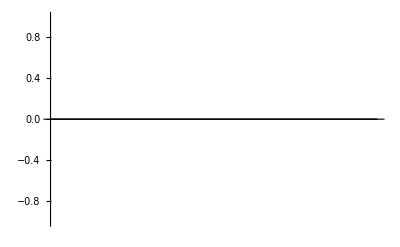

```mathematica
RectangleChart[{
{Subscript[Componentcontribution, GWP LFPC]*0.0601,0.05},
{Subscript[Componentcontribution, GWP LMOC]*0.0662,0.05}
}
]
```

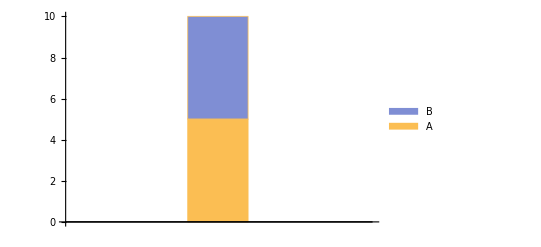

```mathematica
hatchF[mf_List: {#&,#2&},mesh_List: {50,50},style_: GrayLevel[.5],opts:OptionsPattern[]]:=ParametricPlot[{x,y},{x,0,1},{y,0,1},Mesh->mesh,MeshFunctions->mf,MeshStyle->style,BoundaryStyle->None,opts,Frame->False,PlotRangePadding->0,ImagePadding->0,Axes->False]

t1=hatchF[{#-#2&},{30},White,MeshShading->{GrayLevel[.8],GrayLevel[.5]}];
t2=hatchF[{#-#2&,#2+#&},{30},Directive[Thick,White],MeshShading->{{GrayLevel[.6],GrayLevel[.8]}}];

ChartLegends->Placed[SwatchLegend[Automatic,{Style["Aluminium","Arial",16],Style["Cobalt","Arial",16],Style["Copper","Arial",16],Style["Gold","Arial",16],Style["Iron","Arial",16],Style["Manganese","Arial",16],Style["Nickel","Arial",16],Style["Steel","Arial",16],Style["Titanium","Arial",16],Style["Electrolyte","Arial",16],Style["Graphite","Arial",16],Style["Lithium","Arial",16],Style["Plastics","Arial",16],Style["Not recovered","Arial",16]},Spacings->0.5,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LegendLayout->{"ReversedColumn",1}],Right],

BarChart[
{Style[5,Texture@t1],Style[5,Texture@t2]},
ChartLayout->"Stacked",
ChartLegends->{Automatic,{"A","B"}},
ChartElementFunction->System`BarFunctionDump`TextureBar
]
```

```mathematica
Rasterize[ImageResolution->1000];

{"Positive electrode","Negative electrode","Electrolyte","Separator","Cell container","Final cell assembly and transportation","BMS","Module packaging","Final module assembly and transportation","Battery inverter"};

{"RGB 185 0 0","RGB 160 27 16","RGB 160 44 29","RGB 170 65 45","RGB 170 83 62","RGB 170 101 81","RGB 56 87 35","RGB 169 209 142","RGB 226 240 217","RGB 31 78 121"};

{"RGB 128 0 0","RGB 185 0 0","RGB 191 10 48","RGB 230 55 87","RGB 237 41 65","RGB 240 128 128","RGB 56 87 35","RGB 169 209 142","RGB 226 240 217","RGB 31 78 121"};

"RGB 112 48 160","RGB 31 78 121","RGB 0 112 192";
{"RGB 31 78 121","RGB 0 112 192","RGB 112 48 160"}

Interpreter["Color"][{"RGB 82 82 82","RGB 105 105 105","RGB 232 95 59","RGB 128 128 128","RGB 169 169 169","RGB 192 192 192","RGB 211 211 211","RGB 220 220 220","RGB 255 192 0","RGB 255 220 80","RGB 84 130 53","RGB 169 209 142","RGB 118 113 113","RGB 175 171 171"}],
```

```mathematica
SphericalPlot3D[1 , {u, 0, Pi}, {v, 0, 2 Pi}, Mesh -> None, 
 TextureCoordinateFunction -> ({#5, 1 - #4} &), 
 PlotStyle -> Directive[Specularity[White, 10], ], Lighting -> "Neutral", 
 Axes -> False, RotationAction -> "Clip"]
```

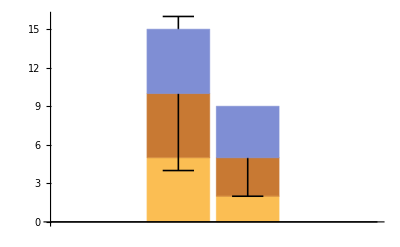

```mathematica
BarChart[{{5,5->6,5},
{2,3->3,4}},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,errorBar[],Automatic}]
```

```mathematica
ChartStyle->Interpreter["Color"][]
```

```mathematica
ClearAll[errorBar]
errorBar[type_: "Rectangle"]:=Module[{error=If[#3==={},0,#3[[1]]],x0=#[[1,1]],x1=#[[1,2]],y1=#[[2,2]]},{ChartElementData[type][##],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]&
```

```mathematica
Test={5,5,5,1};
Test1={2,2,2,2};
Testbis={3,2,5,4};
```

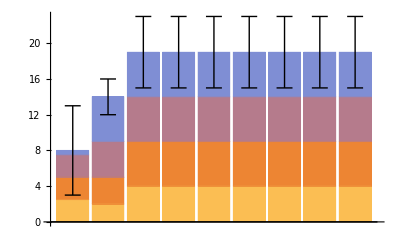

```mathematica
BarChart[{Test/Test1->5,{2,3,4,5->2},{4,5,5,5->4},{4,5,5,5->4},{4,5,5,5->4},{4,5,5,5->4},{4,5,5,5->4},{4,5,5,5->4},{4,5,5,5->4}},
ChartLayout->"Stacked",
ChartElementFunction->{Automatic,Automatic,Automatic,errorBar[]}]
```

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

BarChart::nonopt: Options expected (instead of ) beyond position 1 in BarChart[{{5,5,5},{5,5,5}},ChartLayout→Stacked,]. An option must be a rule or a list of rules.

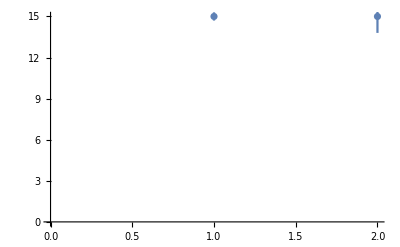
BarChart[{{5,5,5},{5,5,5}},ChartLayout→Stacked,-Graphics-]

```mathematica
Needs["ErrorBarPlots`"]
BarChart[
{{5,5,5},{5,5,5}},
ChartLayout->"Stacked",
ErrorListPlot[
{{{1,15},ErrorBar[0.3]},
{{2,15},ErrorBar[1.2]}},
AxesOrigin->{0,0}]]
```

{2,2,2}

{4,2,1}

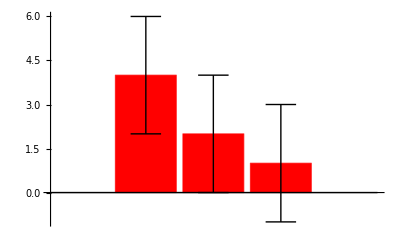

```mathematica
errors={2,2,2}
data={4,2,1}

BarChart[
Thread[data->errors],
ChartStyle->{Red},
ChartElementFunction->errorBar[]]
```

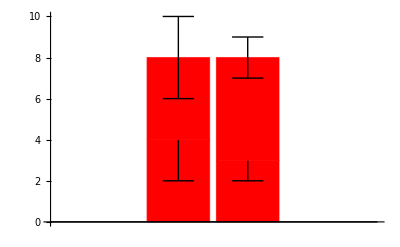

```mathematica
BarChart[
Thread[{{4,4},{3,5}}->{{2,2},{3,1}}],
ChartStyle->{Red},
ChartElementFunction->errorBar[],
ErrorBarFunction->{Green},
ChartLayout->"Stacked"]
```

```mathematica
BarChart[
data,
ChartElementFunction->errorBar["Rectangle"],
ChartLayout->"Stacked"]
```

BarChart::ldata: data is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[data,ChartElementFunction→errorBar[Rectangle],ChartLayout→Stacked]

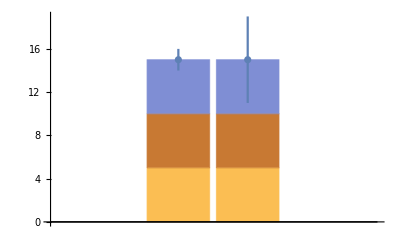

```mathematica
Show[
BarChart[
{{5,5,5},
{5,5,5}},
ChartLayout->"Stacked"],
ErrorListPlot[{{{1,15},ErrorBar[1]},{{2,15},ErrorBar[4]}},
AxesOrigin->{0,0}]]
```

```mathematica
Needs["ErrorBarPlots`"]
ErrorBarPlot[{{10,1},{12,5}}]
```

ErrorBarPlot[{{10,1},{12,5}}]

```mathematica
BarChart[
{5},
ErrorBar[{5,1}]]
```

BarChart::nonopt: Options expected (instead of ErrorBar[{5,1}]) beyond position 1 in BarChart[{5},ErrorBar[{5,1}]]. An option must be a rule or a list of rules.

BarChart[{5},ErrorBar[{5,1}]]

```mathematica
Error
```

```mathematica
ErrorBarPlot
```

ErrorBarPlot

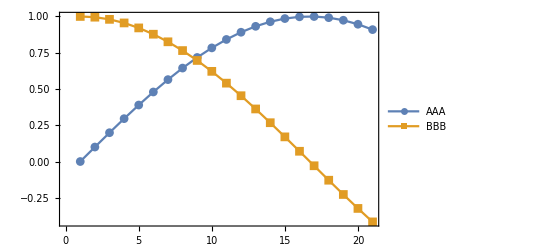

```mathematica
pts=Through[{Sin,Cos}[Range[0,2,0.1]]];
ListPlot[pts,Joined->True,PlotMarkers->Automatic,PlotLegends->Placed[LineLegend[{"AAA","BBB"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{Right,Bottom}],Frame->True]
```

```mathematica
ErrorListPlot[{data,errors}//Transpose,PlotRange->{{0,6},{0,230000}}]
```

Transpose::nmtx: The first two levels of {data,errors} cannot be transposed.

ListPlot::lpn: Transpose[{data,errors}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Transpose[{data,errors}],{PlotRange→{{0,6},{0,230000}}},Method→{OptimizePlotMarkers→False}]

```mathematica
rawData=WeatherData["Saint Louis","MaxTemperature",{{2009,1,1},{2009,12,31},"Day"}]
```

TimeSeries[…]

```mathematica
ends=DayRange[{2009,1,1},{2009,12,31},"EndOfMonth"]
```

{Day: Sat 31 Jan 2009,Day: Sat 28 Feb 2009,Day: Tue 31 Mar 2009,Day: Thu 30 Apr 2009,Day: Sun 31 May 2009,Day: Tue 30 Jun 2009,Day: Fri 31 Jul 2009,Day: Mon 31 Aug 2009,Day: Wed 30 Sep 2009,Day: Sat 31 Oct 2009,Day: Mon 30 Nov 2009,Day: Thu 31 Dec 2009}

```mathematica
filteredDataByMonth=Table[TimeSeriesWindow[rawData,{{2009,k,1},ends[[k]]}],{k,1,12}];
```

```mathematica
meanData=Mean/@filteredDataByMonth
```

{3.6971 °C,9.7975 °C,16.0626 °C,18.4613 °C,24.6987 °C,30.8687 °C,29.1935 °C,29.5716 °C,25.65 °C,16.0019 °C,15.5347 °C,4.49484 °C}

```mathematica
standardError[ts_]:=StandardDeviation[ts]/Sqrt[ts["PathLength"]]
```

```mathematica
stdErrorData=standardError/@filteredDataByMonth
```

{1.24482 °C,1.38533 °C,1.3326 °C,1.07331 °C,0.725073 °C,0.79187 °C,0.414308 °C,0.621351 °C,0.484215 °C,0.75346 °C,0.835263 °C,0.76051 °C}

```mathematica
chartData=Table[meanData[[i]]->stdErrorData[[i]],{i,1,Length[meanData]}]
```

{3.6971 °C→1.24482 °C,9.7975 °C→1.38533 °C,16.0626 °C→1.3326 °C,18.4613 °C→1.07331 °C,24.6987 °C→0.725073 °C,30.8687 °C→0.79187 °C,29.1935 °C→0.414308 °C,29.5716 °C→0.621351 °C,25.65 °C→0.484215 °C,16.0019 °C→0.75346 °C,15.5347 °C→0.835263 °C,4.49484 °C→0.76051 °C}

```mathematica
labels={"Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sept","Oct","Nov","Dec"};
```

```mathematica
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
```

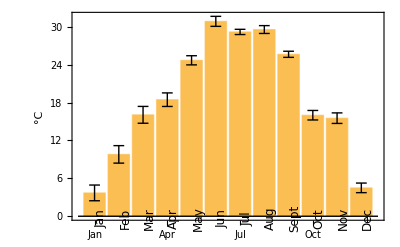

```mathematica
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->Placed[labels,Axis,Rotate[Style[#,12,FontFamily->"Arial"],Pi/2]&],Frame->Left,FrameLabel->Automatic]
```

```mathematica
What is the weather in London?
```